## Pre

This is a recalculation of R. F. Sawyer’s box spectrum in his PRL fast mode paper

Sawyer, R. F. (2016). Neutrino Cloud Instabilities Just above the Neutrino Sphere of a Supernova. Physical Review Letters, 116(8), 1–5. https://doi.org/10.1103/PhysRevLett.116.081101

The actually ELN spectrum dosn’t change the shape or instabilities. I can always put back the length scale in the last step.

Setting Defaults

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/github/neuphysics/codebase/mma/dispersion-relation/sawyer-bs

```mathematica
Get["../../../neupackage/mma/dispersion-relation.wl"]
```

```mathematica
FileNames[]
```

{DR-sawyer-spectrum-001.m,DR-sawyer-spectrum-001.out,DR-sawyer-spectrum.m,DR-sawyer-spectrum.out,DR-sawyer-spectrum-Saw-001.m,DR-sawyer-spectrum-Saw-001.out,DR-sawyer-spectrum-Saw-01.m,DR-sawyer-spectrum-Saw-01.out,DR-sawyer-spectrum-Saw.m,DR-sawyer-spectrum-Saw.out,export,maalsadata-box-spectrum-saw.csv,maalsadata-box-spectrum-s.csv,maarealklsadata-box-spectrum-saw.csv,maarealklsadata-box-spectrum-s.csv,mzamlsadata-box-spectrum-saw.csv,mzamlsadata-box-spectrum-s.csv,mzamrealklsadata-box-spectrum-saw.csv,mzamrealklsadata-box-spectrum-s.csv,mzaplsadata-box-spectrum-saw.csv,mzaplsadata-box-spectrum-s.csv,mzaprealklsadata-box-spectrum-saw.csv,mzaprealklsadata-box-spectrum-s.csv,sawyer-box-spectrum.nb}

Define Plotting Functions

```mathematica
pltDR[spect_]:=Show[
Plot[(#*x)&/@DeleteDuplicates@Flatten[{#[[1]]}&/@spectS],{x,-4.5,4.5},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,ImagePadding->{{20, 70}, {20, 20}},PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLabel->"Dispersion Relation for Spectrum "<>ToString[spect],AspectRatio->1],

ParametricPlot[
{
{n ConAxialSymOmegaNMAA[n,spect],ConAxialSymOmegaNMAA[n,spect]},
{n ConAxialSymOmegaNMZA[n,spect][[1]],ConAxialSymOmegaNMZA[n,spect][[1]]},
{n ConAxialSymOmegaNMZA[n,spect][[2]],ConAxialSymOmegaNMZA[n,spect][[2]]}
},
{n,-50,50},Frame->True,FrameLabel->{"k","ω"},ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLegends->Placed[{"MAA","MZA+","MZA-"},{Left,Top}],PlotLabel->"Dispersion Relation",Exclusions->{1/0.3,1/0.9,1/0.6}]
]
```

```mathematica
pltDRMAAData[spect_,stepsize_:0.01]:=Table[
{n ConAxialSymOmegaNMAA[n,spect],ConAxialSymOmegaNMAA[n,spect]},
{n,-50,50,stepsize}
]
```

```mathematica
pltDRMZApData[spect_,stepsize_:0.01]:=Table[
{n ConAxialSymOmegaNMZA[n,spect][[1]],ConAxialSymOmegaNMZA[n,spect][[1]]},
{n,-50,50,stepsize}
]
pltDRMZAmData[spect_,stepsize_:0.01]:=Table[
{n ConAxialSymOmegaNMZA[n,spect][[2]],ConAxialSymOmegaNMZA[n,spect][[2]]},
{n,-50,50,stepsize}
]
```

## Box Shaped Spectrum from Sawyer

Define Spectrum

```mathematica
uNueBarMin=Cos[ArcSin[0.93]]
alpha=0.77(1/0.93)^2
```

0.36756

0.890276

```mathematica
spectB={{{0,1},1}};
spectS={{{0,uNueBarMin},1},{{uNueBarMin,1},1-alpha}}
```

{{{0,0.36756},1},{{0.36756,1},0.109724}}

Plot DR

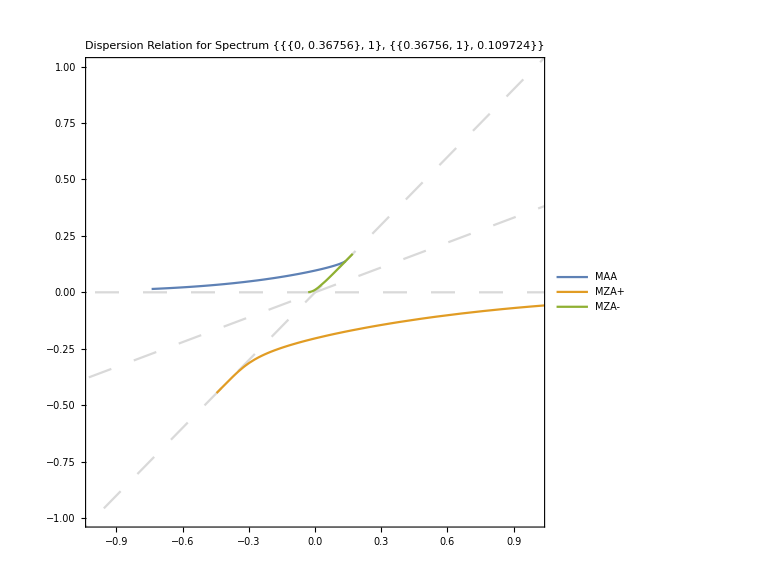

```mathematica
Show[
pltDR[spectS],
PlotRange->{{-1,1},{-1,1}}
]
```

Clean Up LSA

```mathematica
maalsadataS=Import["maalsadata-box-spectrum-saw.csv"];
```

```mathematica
mzaplsadataS={#[[1]],Re@ToExpression@#[[2]],Im@ToExpression@#[[2]]}&/@Import["mzaplsadata-box-spectrum-saw.csv"];
```

```mathematica
mzamlsadataS={#[[1]],Re@ToExpression@#[[2]],Im@ToExpression@#[[2]]}&/@Import["mzamlsadata-box-spectrum-saw.csv"];
```

```mathematica
Dimensions@maalsadataS
Dimensions@mzaplsadataS
Dimensions@mzamlsadataS
```

{90,3}

{90,3}

{90,3}

```mathematica
ConAxialSymOmegaNMAAEqnLHSComplex[0.001,0.1+0.1I,spectS]
ConAxialSymOmegaNMAAEqnLHSComplexN[0.001,0.1+0.1I,spectS]
```

0.00298749-0.00783993 ⅈ

0.00298749-0.00783993 ⅈ

```mathematica
ConAxialSymOmegaNMZApEqnLHSComplexN[0.001000000000000334,1.7429211390553634+8.447118418362738I,spectS]
ConAxialSymOmegaNMZAEqnLHSComplex[0.001,0.1+0.1I,spectS]
```

0.00100552+0.000483505 ⅈ

0.000198898+0.000579502 ⅈ

```mathematica
imaglow=10^(-10);
valepsilon=0.01;
```

```mathematica
maalsadataSClean=Select[Flatten@#&/@maalsadataS,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(imaglow<Abs@#[[3]]<500)&&(Abs@ConAxialSymOmegaNMAAEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectS]<valepsilon)&];
mzaplsadataSClean=Select[Flatten@#&/@mzaplsadataS,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(imaglow<Abs@#[[3]]<500)&&(Abs@ConAxialSymOmegaNMZApEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectS]<valepsilon)&];
mzamlsadataSClean=Select[Flatten@#&/@mzamlsadataS,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(imaglow<Abs@#[[3]]<500)&&(Abs@ConAxialSymOmegaNMZAmEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectS]<valepsilon)&];
```

```mathematica
Dimensions@maalsadataSClean
Dimensions@mzaplsadataSClean
Dimensions@mzamlsadataSClean
```

{0}

{1,3}

{0}

```mathematica
mzamlsadataSClean
```

{}

-Graphics-

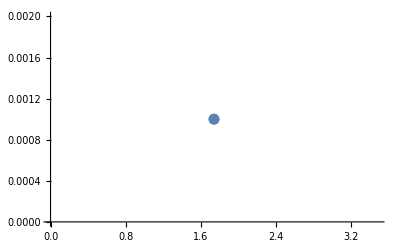

-Graphics-

```mathematica
ListPlot[
{#[[2]],#[[1]]}&/@maalsadataSClean
]
ListPlot[
{#[[2]],#[[1]]}&/@mzaplsadataSClean
]
ListPlot[
{#[[2]],#[[1]]}&/@mzamlsadataSClean
]
```

## Export Data

DR

```mathematica
pltDRMAADataS=Select[pltDRMAAData[spectS,0.01],#[[1]]∈Reals&];//Quiet
```

```mathematica
pltDRMZApDataS=Select[pltDRMZApData[spectS,0.001],#[[1]]∈Reals&];//Quiet
```

```mathematica
pltDRMZAmDataS=Select[pltDRMZAmData[spectS,0.001],#[[1]]∈Reals&];//Quiet
```

```mathematica
pltDRMZADataS=Sort[Join[pltDRMZApDataS,pltDRMZAmDataS],#1[[2]]<#2[[2]]&]
```

{{-1.23979,-1.24103},{-1.18554,-1.18791},{-1.15135,-1.15481},{-1.12573,-1.13025},101991,{0.417348,0.418604},{0.447003,0.447899},{0.49621,0.496707}}
 |  |  |  |

Export Data

```mathematica
Export["export/pltDRMAADataS.csv",pltDRMAADataS]
Export["export/pltDRMZApDataS.csv",pltDRMZApDataS]
Export["export/pltDRMZAmDataS.csv",pltDRMZAmDataS]
Export["export/pltDRMZADataS.csv",pltDRMZADataS]
Export["export/maalsadataSClean.csv",maalsadataSClean]
Export["export/mzaplsadataSClean.csv",mzaplsadataSClean]
Export["export/mzamlsadataSClean.csv",mzamlsadataSClean]
```

export/pltDRMAADataS.csv

export/pltDRMZApDataS.csv

export/pltDRMZAmDataS.csv

export/pltDRMZADataS.csv

export/maalsadataSClean.csv

export/mzaplsadataSClean.csv

export/mzamlsadataSClean.csv